```mathematica
ClearAll["Global`*"]
```

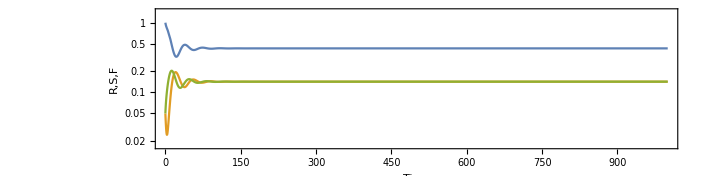

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==1,X[0]==0.05,Y[0]==0.05},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,λ=0.2,σ=0.5,ρ=0.2,μ=0.2,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,μ,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

A version without the starving class...

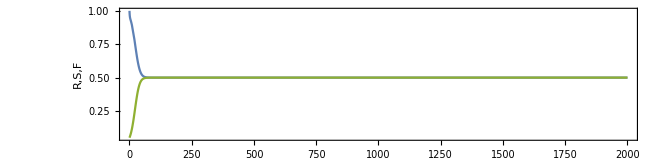

```mathematica
MetapopDyn[a_,λ_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -( Y[t])*R[t] ,
Y'[t] ==λ*Y[t]*R[t]- μ*Y[t](1-R[t]),
R[0]==1,Y[0]==0.05},{R,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=1,λ=0.1,μ=0.1,T=2000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(X+Y),
0==σ*(1-R)*Y-ρ*R*X-μ*X, 
0==λ*Y-σ*(1-R)*Y+ρ*R*X},
{R,X,Y}]]
```

{{R→0,X→0,Y→0},{R→1,X→0,Y→0},{R→(μ (-λ+σ))/(λ ρ+μ σ),X→(α λ^2 (μ+ρ))/((λ+μ) (λ ρ+μ σ)),Y→(α λ μ (μ+ρ))/((λ+μ) (λ ρ+μ σ))}}

```mathematica
InternalSol1 = Sol[[3]];
(*InternalSol2 = Sol[[4]];*)
```

```mathematica
{InternalSol1}/.{α->0.5,λ->0.1,μ->0.2,ρ->0.5,σ->0.5}
```

{{R→0.533333,X→0.0777778,Y→0.155556}}

This means only InternalSol2 is an INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

```mathematica
Rstar = IntPosSol[[1]][[2]]
Xstar = IntPosSol[[2]][[2]]
Ystar = IntPosSol[[3]][[2]]
```

(μ (-λ+σ))/(λ ρ+μ σ)

(α λ^2 (μ+ρ))/((λ+μ) (λ ρ+μ σ))

(α λ μ (μ+ρ))/((λ+μ) (λ ρ+μ σ))

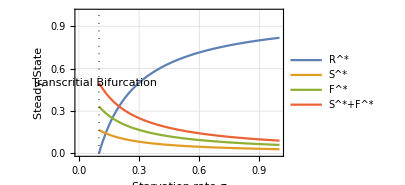

```mathematica
With[{alpha=0.5,lambda=0.1,mu=0.2,rho=0.2},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
FigFP=
Show[{
Plot[{Rstarspec,Xstarspec,Ystarspec,Xstarspec+Ystarspec},{σ,lambda,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","Steady State"},PlotRange->{{0,1},{0,1}},ImageSize->300,PlotLegends->{"R^*","S^*","F^*","S^*+F^*"}],
Graphics[{Dotted,Line[{{lambda,0},{lambda,1}}]}],
Graphics[Rotate[Text["Transcritial Bifurcation",{(lambda-0.02),0.5}],90Degree]]
}]
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf",FigFP]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/Manuscript/fig_FP.pdf

```mathematica
Limit[{Rstarspec,Xstarspec,Ystarspec},σ->Infinity]
```

{1.,0.,0.}

```mathematica
dR=   α*R*(1-R)-R*(X+Y);
dX =σ*(1-R)*Y-ρ*R*X-μ*X;
dY =λ*Y-σ*(1-R)*Y+ρ*R*X;
JacSpec = {
{D[dR,R],D[dR,X],D[dR,Y]},
{D[dX,R],D[dX,X],D[dX,Y]},
{D[dY,R],D[dY,X],D[dY,Y]}
}
```

{{-X-Y+(1-R) α-R α,-R,-R},{-X ρ-Y σ,-μ-R ρ,(1-R) σ},{X ρ+Y σ,R ρ,λ-(1-R) σ}}

```mathematica
JacSpec//MatrixForm
```

(-X-Y+(1-R) α-R α | -R | -R
-X ρ-Y σ | -μ-R ρ | (1-R) σ
X ρ+Y σ | R ρ | λ-(1-R) σ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,X->Xstar,Y->Ystar};
```

```mathematica
JacSpecSol
```

{{-(α λ^2 (μ+ρ))/((λ+μ) (λ ρ+μ σ))-(α λ μ (μ+ρ))/((λ+μ) (λ ρ+μ σ))-(α μ (-λ+σ))/(λ ρ+μ σ)+α (1-(μ (-λ+σ))/(λ ρ+μ σ)),-(μ (-λ+σ))/(λ ρ+μ σ),-(μ (-λ+σ))/(λ ρ+μ σ)},{-(α λ^2 ρ (μ+ρ))/((λ+μ) (λ ρ+μ σ))-(α λ μ (μ+ρ) σ)/((λ+μ) (λ ρ+μ σ)),-μ-(μ ρ (-λ+σ))/(λ ρ+μ σ),σ (1-(μ (-λ+σ))/(λ ρ+μ σ))},{(α λ^2 ρ (μ+ρ))/((λ+μ) (λ ρ+μ σ))+(α λ μ (μ+ρ) σ)/((λ+μ) (λ ρ+μ σ)),(μ ρ (-λ+σ))/(λ ρ+μ σ),λ-σ (1-(μ (-λ+σ))/(λ ρ+μ σ))}}

```mathematica
({R,X,Y}/.Sol)/.{α->alpha,λ->lambda,μ->mu,ρ->rho,σ->sigma}
```

{{0,0,0},{1,0,0},{(mu (-lambda+sigma))/(lambda rho+mu sigma),(alpha lambda^2 (mu+rho))/((lambda+mu) (lambda rho+mu sigma)),(alpha lambda mu (mu+rho))/((lambda+mu) (lambda rho+mu sigma))}}

This plot shows that the bifurcation at lambda=sigma is a Transcritical (I think)

```mathematica
Jac2=JacSpec/.Sol[[2]]
```

{{-α,-1,-1},{0,-μ-ρ,0},{0,ρ,λ}}

```mathematica
Manipulate[
Eig = Eigenvalues[JacSpecSol/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,σ->sigma}];
REig = Re[Eig];
IEig = Im[Eig];
Row[{
Show[{
ListPlot[Transpose[{REig,IEig}],PlotRange->{{-1,1},{-1,1}}],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"}],
FP=({R,X,Y}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,σ->sigma};
Show[{
ListPointPlot3D[FP,
PlotStyle->Directive[{ColorData[97,4],PointSize[Large]}],PlotLabel->FP,PlotRange->{{-1,1},{0,1},{0,1}},ImageSize->300,AxesLabel->{"R^*","S^*","F^*"}],
Graphics3D[{Opacity[0.5],Polygon[{{0,0,0},{0,1,0},{0,1,1},{0,0,1}}]}]
}]
}],
{{sigma,0.1},0,0.2,0.001}]
```

```mathematica
FP
```

{{0,0,0},{1,0,0},{0.,0.166667,0.333333}}

Specific Bifurcations

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,σ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,μ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,α]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,ρ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,λ]
```

{{σ→λ}}

{{μ→0},{μ→-ρ}}

{{α→0}}

{{ρ→-μ}}

{{λ→0},{λ→σ}}

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,muy];
```

$Aborted

```mathematica
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
```

```mathematica
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
```

```mathematica
HopfAnalytic = Solve[Det[Sylv]==0,λ];
```

```mathematica
HopfAnalytic
```

{{λ→σ},{λ→-(α μ-μ ρ-ρ^2-2 ρ σ)/(4 ρ)-1/2 1-1/2 √((1)^2/(2 ρ^2)-1/ρ-1-1-1^1/(3 2^1 ρ^2)-(-1^3/ρ^3+1/ρ^2-(8 1)/ρ^2)/(4 √1))},{1},{λ→1},{λ→-(α μ-μ ρ-ρ^2-2 ρ σ)/(4 ρ)+1/2 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(4 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ+(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)+(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (7+√(-4 (1)^3+(1)^2))^(1/3))+((7+√(-4 (1^2-1+1)^3+(1)^2))^(1/3))/(3 2^(1/3) ρ^2))+1/2 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(2 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ-(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)-(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (7+√(-4 ((1)^2-1+12 ρ^2 (1))^3+(1)^2))^(1/3))-1/(3 2^(1/3) ρ^2)(2 (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^3-9 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+1+1-72 ρ^2 (1) (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)+√(-4 (1)^3+(1)^2))^(1/3)+(-((α μ-μ ρ-ρ^2-2 ρ σ)^3)/ρ^3+(4 (α μ-μ ρ-ρ^2-2 ρ σ) (-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2))/ρ^2-(8 (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2))/ρ^2)/(4 √(((α μ-μ ρ-ρ^2-2 ρ σ)^2)/(4 ρ^2)-(-2 α μ σ-4 μ^2 σ-4 μ ρ σ+ρ σ^2)/ρ+(-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)/(3 ρ^2)+(2^(1/3) ((-2 α μ ρ σ-4 μ^2 ρ σ-4 μ ρ^2 σ+ρ^2 σ^2)^2-3 (α μ ρ-μ ρ^2-ρ^3-2 ρ^2 σ) (-α μ^3 σ-α μ^2 ρ σ-μ^3 σ^2+α μ ρ σ^2+μ^2 ρ σ^2+2 μ ρ^2 σ^2)+12 ρ^2 (α μ^3 σ^2+μ^4 σ^2+α μ^2 ρ σ^2+2 μ^3 ρ σ^2+μ^2 ρ^2 σ^2)))/(3 ρ^2 (7+√(-4 ((1)^2-1+1)^3+(1)^2))^(1/3))+((7+√(-4 ((1)^2-1+12 ρ^2 (1))^3+(1)^2))^(1/3))/(3 2^(1/3) ρ^2))))}}
 |  |  |  |

```mathematica
FullSimplify[HopfAnalytic]
```

$Aborted

The solution to the Hopf Bifurcation surface may not be analytically tractable
Try Solving numerically with a = 1

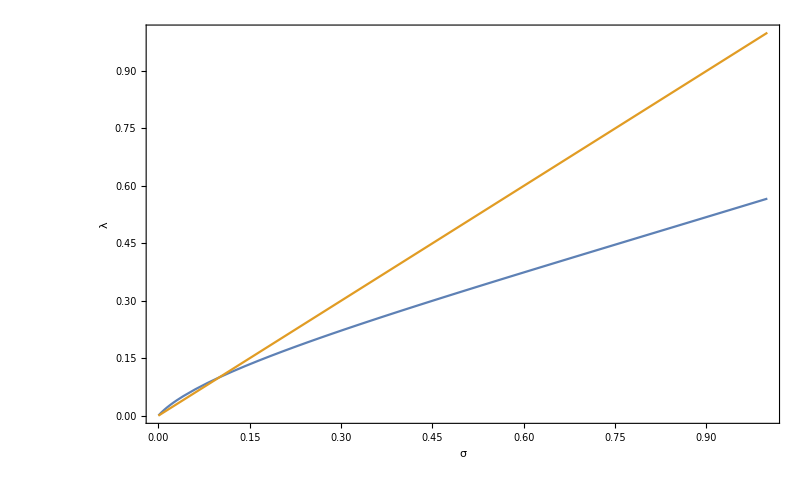

```mathematica
Hsp = HopfAnalytic/.{α->0.5,μ->0.2,ρ->0.2};
Plot[{λ/.Hsp[[4]],σ},{σ,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"σ","λ"}]
```

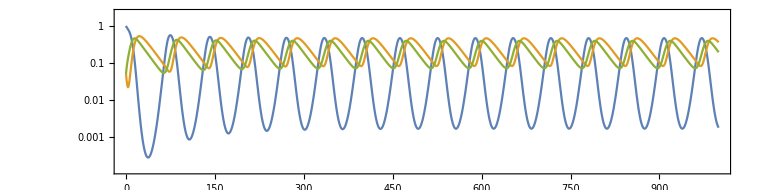

```mathematica
MetapopDyn[a_,λ_,σ_,ρ_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(X[t] + Y[t])*R[t] ,
X'[t] ==σ*(1-R[t])*Y[t] - ρ* R[t]*X[t] - μ*X[t],
Y'[t] ==λ*Y[t]-σ*(1-R[t])*Y[t] +ρ* R[t] * X[t],
R[0]==1,X[0]==0.05,Y[0]==0.05},{R,X,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.5,σ=0.3,λ=0.25,ρ=0.2,μ=0.2,T=1000},
Traj=Evaluate[{R[t],X[t],Y[t]}/.MetapopDyn[a,λ,σ,ρ,μ,T] ];
LogPlot[Traj,{t,0,T},PlotRange->{0,1},AspectRatio->0.25,Frame->True]
]
```

```mathematica
Hsp2 =HopfAnalytic/.{α->0.5,ρ->0.2};
Plot3D[{σ,λ/.Hsp2[[4]]},{σ,0,1},{μ,0,1},PlotRange->{0,1}, ClippingStyle->None,PlotStyle->{Directive[ColorData[97,1],Opacity[0.8]],Directive[ColorData[97,2],Opacity[0.8]]},Mesh->None,AxesLabel->{"σ","μ","λ"},PlotLegends->{"SN","Hopf"},Lighting->{{"Ambient", White}}]
```

-Graphics3D-

```mathematica
HopfData = Table[{σ,Re[N[λ/.Hsp[[4]]]]},{σ,0.1,1,0.01}];
(*HopfData=Join[{Reverse[HopfNumSol2down,2]/.σ->"NA",Reverse[HopfNumSol2up,2]/.σ->"NA"}];*)
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv",HopfData,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/HopfData.csv

```mathematica
Hsp2LS = Hsp2[[4]]/.σ->λ;
```

```mathematica
co2NUM  = Table[NSolve[λ/.Hsp2LS,μ],{λ,0.1,1,0.1}]
```

$Aborted

```mathematica
PS = λ/.Hsp2LS;
NSolve[0.5==PS/.λ->0.5,μ]
```

{}